```mathematica
a = -1
b = 3
n = 9
h = (b-a)/(n-1)
z = (a - h)
X =Table[z += h, n]
i = 1
f[x_]:=-Sin[4-x^2]
Y = Table[f[X[[i]]], n]
Y
```

-1

3

9

1/2

-3/2

{-1,-1/2,0,1/2,1,3/2,2,5/2,3}

1

{-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3]}

{-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3],-Sin[3]}

```mathematica
For[i = 1, i ≤ n, i++, Y[[i]] = f[X[[i]]]];
Y
X
```

Y

X

```mathematica
F=0;
S=1;
For[i=1,i≤n,i++,{
S=Y[[i]];
For[j=1,j≤n,j++,{
If[j≠i,S*=((x-X[[j]])/(X[[i]]-X[[j]]))]
}];
F+=S;
}]

N[Collect[F,x]]
```

0.756802-0.342169 x-0.117024 x^2+1.45396 x^3-3.03165 x^4-0.0842725 x^5+2.10783 x^6-1.02752 x^7+0.142925 x^8

-16/45 (5/2-x) (-3+x) (-2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[7/4]-16/315 (-3+x) (-2+x) (-3/2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[9/4]+2/315 (1-x) (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) x (1/2+x) Sin[3]-4/9 (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) x (1/2+x) (1+x) Sin[3]-16/315 (1/2-x) (3/2-x) (5/2-x) (-3+x) (-2+x) (-1+x) x (1+x) Sin[15/4]+16/45 (3/2-x) (5/2-x) (-3+x) (-2+x) (-1+x) x (1/2+x) (1+x) Sin[15/4]+8/45 (1-x) (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) (1/2+x) (1+x) Sin[4]+2/315 (-5/2+x) (-2+x) (-3/2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[5]

{-Sin[3],-Sin[15/4],-Sin[4],-Sin[15/4],-Sin[3],-Sin[7/4],0,Sin[9/4],Sin[5]}

{-Sin[3],-Sin[15/4],-Sin[4],-Sin[15/4],-Sin[3],-Sin[7/4],0,Sin[9/4],Sin[5]}

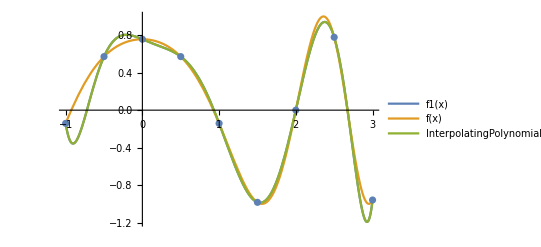

1

(Abs[(-3+x) (-5/2+x) (-2+x) (-3/2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x)] Sin[9/4])/3628800

```mathematica
f1[x_]:=-16/45 (5/2-x) (-3+x) (-2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[7/4]-16/315 (-3+x) (-2+x) (-3/2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[9/4]+2/315 (1-x) (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) x (1/2+x) Sin[3]-4/9 (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) x (1/2+x) (1+x) Sin[3]-16/315 (1/2-x) (3/2-x) (5/2-x) (-3+x) (-2+x) (-1+x) x (1+x) Sin[15/4]+16/45 (3/2-x) (5/2-x) (-3+x) (-2+x) (-1+x) x (1/2+x) (1+x) Sin[15/4]+8/45 (1-x) (2-x) (3-x) (-5/2+x) (-3/2+x) (-1/2+x) (1/2+x) (1+x) Sin[4]+2/315 (-5/2+x) (-2+x) (-3/2+x) (-1+x) (-1/2+x) x (1/2+x) (1+x) Sin[5];
Y2 = Table[0,n];
For[i=1,i≤n,i++,{Y2[[i]]=f1[X[[i]]]}];
Print[Y];
Print[Y2];
Show[Plot[{f1[x],
f[x],
InterpolatingPolynomial[{{-1,-Sin[3]},{-1/2,-Sin[15/4]},{0,-Sin[4]},{1/2,-Sin[15/4]},{1,-Sin[3]},{3/2,-Sin[7/4]},
{2,0},{5/2,Sin[9/4]},{3,Sin[5]}},x]
},{x,a,b},PlotLegends->"Expressions"],ListPlot[{{X[[1]],Y[[1]]},{X[[2]],Y[[2]]},{X[[3]],Y[[3]]},{X[[4]],Y[[4]]},{X[[5]],Y[[5]]},
{X[[6]],Y[[6]]},{X[[7]],Y[[7]]},{X[[8]],Y[[8]]},{X[[9]],Y[[9]]}}]]
Mxplus1=0;
For[i=1,i≤n,i++,{If[(f[X[[i]]])^(n+1)>Mxplus1,Mxplus1=f[X[[i]]]]}];
S=1
For[i=1,i≤n,i++,S*=(x-X[[i]])];
Rnxmax = Mxplus1/Factorial[n+1]*Abs[S];
Print[Rnxmax];
```